# Stability analyses under accelerating returns

```mathematica
Clear["Global`*"]; 
SetDirectory[NotebookDirectory[]];
```

## 1. Functions

```mathematica
blue=RGBColor["#0A71B7"]
orange= RGBColor["#D25F02"]
```

RGBColor[0.0392156862745098, 0.44313725490196076, 0.7176470588235294]

RGBColor[0.8235294117647058, 0.37254901960784315, 0.00784313725490196]

```mathematica
Functions = { Bc->Function[k,n (k/n)^u β]};
```

```mathematica
values={n->4,β->1,Cc-> 0.3,δ->1,u->2,cd-> 0.5} ;

cm=72/2.54;
```

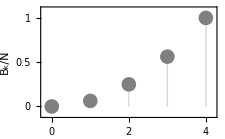

```mathematica
graphicspPayoffs=ListPlot[Table[{k,(k/n)^u β  }/.values,{k,0,4}],Filling->Axis,PlotStyle->Gray,Frame->True,FrameTicks->{{{0,0.5,1},None},{{0,1,2,3,4},None}},ImageSize->8cm,FrameLabel->{k,Rotate[Subscript[B, k]/N,-Pi/2]},LabelStyle->Directive[FontFamily->"Arial",FontSize->17,Black],PlotMarkers->{Automatic,15},PlotRange-> {{-0.2,4.2},{-0.1,1.1}}]
```

Figure 3a of the main text

```mathematica
Export["Payoff_Acc.pdf",Show[graphicspPayoffs,ImageSize->8 cm]]
```

Payoff_Linear.pdf

## 2. Numerical analyses

The function below performs numerical stability analyses,looking for a value of x=(z,d_0,...,d_N) where directional selection is null on all traits. We also compute the singular value under unconditional dispersal(when d_0=d_1=...=d_N). To do so, we use the Mathematica function "FindRoot". This corresponds to the procedure described in section 3.3 of the main text and section D.3.1 of the Appendix. We also compute whether the singular strategy found is convergence stable by computing the eigenvalues if the Jacobian Matrix at the singular strategy (procedure described in Appendix D.3.2. The function returns the singular probability of cooperation,which we will then plot using another function. It will also print "convergence stable" if the largest  eigenvalues of Jacobian is negative. If none is stable (as this is the case here), it will print "All singular strategies are convergence unstable".

```mathematica
(****** Define the important functions *******)
Pk0[k_,z_,n_]:=z^k(1-z)^(n-k)Binomial[n,k];(* Probability that there is k cooperators among n individuals when the population is monomorphic for z *)
fec[k_,j_]:=(1+δ (Bc[k]/n-Cc j)); (* fecundity of an individual either cooperating (j=1) or defecting (j=0) in a group with k cooperators *)
fecpatch[k_]:=(1+ δ((k /n)(Bc[k]/n-Cc )+(1-k/n)(Bc[k]/n)));
(* average fecundity in a patch with k cooperators*)
fecphilo[k_]:=fecpatch[k](1-d[k]);(* offspring produced that will remain in their local patch *)
fecdisp[z_]:= ∑_(k2=0)^n d[k2] (1-cd) fecpatch[k2]Pk0[k2,z,n];
fecloc=( (1-d[1,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c1]/n+ (1-d[2,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c2]/n+(1-d[3,c1+c2+c3+c0])fec[c1+c2+c3+c0,c3]/n+(1-d[c1+c2+c3+c0]) ((n-3-c0)fec[c1+c2+c3+c0,0]/n+c0 fec[c1+c2+c3+c0,1]/n) );
(* number of offspring coming into an arbirary patch when the population is monomorphic for z *)
wdef=∑_(c0=0)^(n-3) ∑_(c3=0)^1 ∑_(c2=0)^1 ∑_(c1=0)^1 fec[c1+c2+c3+c0,c1]((  1-d[1,c1+c2+c3+c0])/(fecloc+ fecdisp[d[n+1]]) + ∑_(k0=0)^n ((d[1,c1+c2+c3+c0](1-cd) )/( fecphilo[k0]+ fecdisp[d[n+1]]))Pk0[k0,d[n+1],n])d[1,n+1]^c1(1-d[1,n+1])^(1-c1) d[2,n+1]^c2(1-d[2,n+1])^(1-c2)d[3,n+1]^c3(1-d[3,n+1])^(1-c3) Pk0[c0,d[n+1],n-3];
(* Fitness of a focal individual*)
```

```mathematica
Calczval[βval_,Ccval_,δval_,nval_,cdvect_,uval_]:=(
values={n->nval,β->βval,Cc-> Ccval,δ->δval,u->uval} ;
valuesNeutral={n->nval,δ->0} ;
Functions = { Bc->Function[k,n(k/n)^u β]};
m[k0_]:=fecdisp[d[n+1]] /(fecphilo[k0]+fecdisp[d[n+1]] )/.valuesNeutral;
monopop=Flatten[Table[{ d[i,k]-> d[k]},{k,0,nval+1},{i,1,3}]];
uncond1=Flatten[Table[{ d[i,k]-> d[i,0]},{k,0,nval},{i,1,3}]];
uncond2=Flatten[Table[{ d[k]-> d[0]},{k,0,nval} ]];
w=wdef/.Functions/.values;
(* Fitness of a focal individual*)
solR2=Flatten[Solve[(R2 == ∑_(c0=0)^n (1-m[c0])^2(1/n+((n-1)/n)R2)Pk0[c0,d[n+1],n]/.valuesNeutral/.Functions//.valuesNeutral),R2]];
solR2R={R2R->1/n+((n-1)/n)R2/.solR2};
SUncondi=
Table[
D[w/.uncond1 /.uncond2, d[1,k]]+ (n-1)R2 D[w/.uncond1/.uncond2, d[2,k]]/. solR2 /. monopop /.uncond2/.values
,{k,{0,nval+1}}];
SCondi=Table[
D[w, d[1,x]]+ (n-1)R2 D[w, d[2,x]]/. solR2 /. monopop /.values
,{x,0,nval+1}];
res=Table[
cc=0;
d0baseline=2/(1+2 cd n+√(1+4 cd^2 (-1+n) n))/.values/.cd->cdtab;
SUncondiTab=Evaluate[SUncondi/.cd->cdtab/.u->utab];
equiUncondi=FindRoot[Table[SUncondiTab[[i]]==0,{i,1,2}], {d[0],d0baseline,0,1},{d[nval+1],If[cdtab==cdvect[[1]],0.75,zUncondi ]  }] ;
zUncondi = Last[equiUncondi][[2]];
d0 = First[equiUncondi][[2]];
SCondiTab=Evaluate[SCondi/.cd->cdtab/.u->utab];
equiCondi=FindRoot[Table[SCondiTab[[i]]==0,{i,1,nval+2}], Append[ Table[ {d[k],d0baseline},{k,0,nval}] ,{d[nval+1], If[cdtab==0.05,zUncondi,zCondi ]  }]] ;
zCondi = Last[equiCondi][[2]];

JTabUncondi=D[SUncondiTab,{Table[ d[k],{k,{0,nval+1}}]}]/.equiUncondi;
JmaxUncondi=Re[Eigenvalues[JTabUncondi]]//Max;
If[JmaxUncondi<0,Print["convergence stable"];cc=1];
JTabCondi=D[SCondiTab,{Table[ d[k],{k,0,nval+1}]}]/.equiCondi;
JmaxCondi=Re[Eigenvalues[JTabCondi]]//Max;
If[JmaxCondi<0,Print["convergence stable"];cc=1];
{cdtab, zUncondi,zCondi}
,{cdtab,cdvect}];
If[cc==0,Print["All singular strategies are convergence unstable"]];
Transpose[res]);
```

```mathematica
cdv=Subdivide[0.05,0.95,18]
```

{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95}

```mathematica
Calczval[1.,0.3,1.,4,cdv,2]
```

All singular strategies are convergence unstable

{{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95},{0.6356,0.640781,0.646754,0.652367,0.657243,0.661362,0.664821,0.667736,0.67021,0.672329,0.674158,0.675751,0.677148,0.678384,0.679483,0.680466,0.681351,0.682152,0.682879},{0.615868,0.57402,0.524086,0.475694,0.432415,0.39488,0.362634,0.334934,0.311041,0.29031,0.272204,0.256287,0.242206,0.229673,0.218456,0.208364,0.199241,0.190957,0.183403}}

```mathematica
(*The following function plot the singular value of cooperation, in orange in the presence of socially-mediated dispersal and in grey in its absence*)
PlotHelp[βval_,Ccval_,δval_,nval_,cdvect_,uval_,shape_,size_]:=(
x0=Calczval[βval,Ccval,δval,nval,cdvect,uval];
p1=ListPlot[ Transpose[{cdvect,x0[[2]]}],PlotMarkers->Style[shape,size],PlotStyle->Gray];
p2=ListPlot[  Transpose[{cdvect,x0[[3]]}],PlotMarkers->Style[shape,size],PlotStyle->orange];
Show[p2,p1,LabelStyle->Directive[FontFamily->" Arial",FontSize->12,Black],FrameTicks->{{{0,0.25,.5,0.75},None},{{0,.5,1},None}},Frame->True,PlotRange->{{0,1},{-0.01,0.85}},AspectRatio->0.85,FrameLabel->{None,"z^*"},RotateLabel->False])
```

All singular strategies are convergence unstable

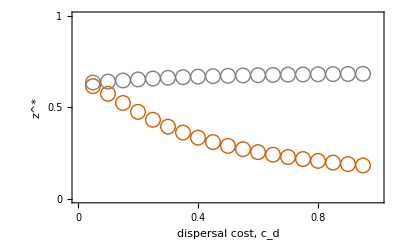

```mathematica
p2=Show[PlotHelp[1.,0.3,1.,4,cdv,2,○,15],AspectRatio->0.6,PlotRangePadding->0,FrameTicks->{{{0,.5,1},None},{{0,.2,.4,.6,.8,1},None}},PlotRange->{{0,1},{0,1}},FrameLabel->{"dispersal cost, c_d","z^*"},LabelStyle->Directive[FontFamily->"Arial",FontSize->16,Black]]
```

```mathematica
Export["Acc_main.pdf",p2,ImageSize->11cm]
```

Acc_main.pdf

All singular strategies are convergence unstable

All singular strategies are convergence unstable

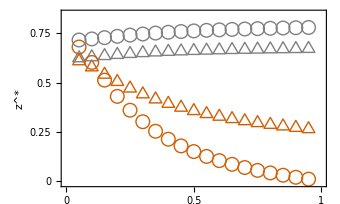

```mathematica
p25=PlotHelp[1.,0.3,1.,4,cdv,1.5,○,14];
p15=PlotHelp[1.,0.3,1.,4,cdv,2.5,△,15];
plot=Show[p15,p25,AspectRatio->0.6,ImageSize->12cm]
```

```mathematica
Export["Acc_u.pdf",plot,ImageSize->12cm]
```

Acc_u.pdf

FindRoot::jsing: Encountered a singular Jacobian at the point {d[0],d[1],d[2],d[3],d[4],d[5],d[6],d[7]} = {0.109173,0.152848,0.228192,0.23164,-0.153417,-4.52638,0.10943,0.000953487}. Try perturbing the initial point(s).

General::munfl: (-1.02458×10^-31)^10 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.85614×10^-187 (-2.61766×10^-124) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.92807×10^-186 (-2.61766×10^-124) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

All singular strategies are convergence unstable

All singular strategies are convergence unstable

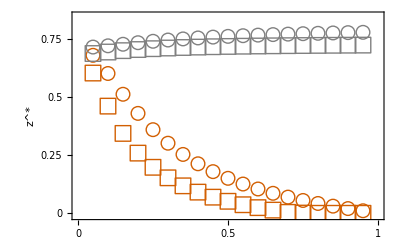

```mathematica
p6=PlotHelp[1.5,0.3,1.,6,cdv,1.5,□,16];
p4=PlotHelp[1.0,0.3,1.,4,cdv,1.5,○,14];
plot=Show[p4,p6,AspectRatio->0.6]
(*Due to the fact that the singular value of z is sommetimes close to 0, there may be some error message when using the function FindRoot (precision may be lost). The function still works as intended*)
```

```mathematica
Export["Acc_N.pdf",plot,ImageSize->12cm]
```

Acc_N.pdf

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

All singular strategies are convergence unstable

All singular strategies are convergence unstable

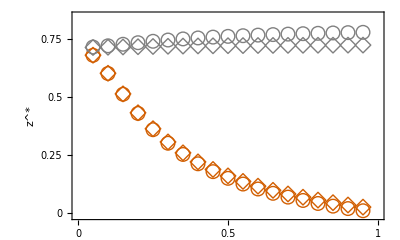

```mathematica
p1d=PlotHelp[1.0,0.3,.1,4,cdv,1.5,◇,16];
p15=PlotHelp[1.0,0.3,1.,4,cdv,1.5,○,14];
plot=Show[p15,p1d,AspectRatio->0.6]
(*Due to the fact that the singular value of z is sommetimes close to 0, there may be some error message when using the function FindRoot (precision may be lost). The function still works as intended*)
```

```mathematica
Export["Acc_delta.pdf",plot,ImageSize->12cm]
```

Acc_delta.pdf